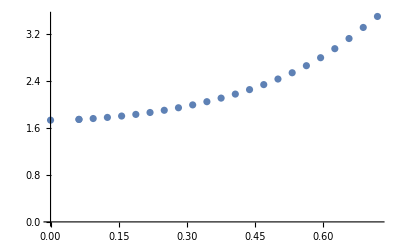

```mathematica
a={{0,1.732201},{0.062500,1.745196},{0.062500,1.745196},{0.093750,1.759997},{0.125000,1.779063},{0.156250,1.802409},{0.187500,1.830239},{0.218750,1.862834},{0.250000,1.900494},{0.281250,1.943496},{0.312500,1.992120},{0.343750,2.046737},{0.375000,2.107867},{0.406250,2.176155},{0.437500,2.252370},{0.468750,2.337458},{0.500000,2.432616},{0.531250,2.539356},{0.562500,2.659563},{0.593750,2.795468},{0.625000,2.949327},{0.656250,3.122243},{0.687500,3.310687},{0.718750,3.497894}};
ListPlot[a]
```

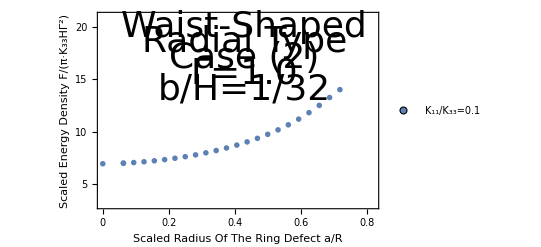

```mathematica
aa=a*Table[{1,4},{i,0,23}];
ListPlot[{aa},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{5,10,15,20},None},{{0,0.2, 0.4, 0.6, 0.8},None}}, PlotRange->{{0,0.82},{3,21}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{0.43,20}],Text[Style["Radial Type",Directive[Black,36]],{0.43,18.5}],Text[Style["Case (2)",Directive[Black,36]],{0.43,17}],Text[Style["Γ=1.0",Directive[Black,36]],{0.43,15.5}],Text[Style["b/H=1/32",Directive[Black,36]],{0.43,14}]}]
```